```mathematica
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]
```

```mathematica
Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-L IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]

SmashEigen[G0_,S0_]:=Module[{G=G0,S=S0},
Eigenvalues[Smash[G,S]]
]
```

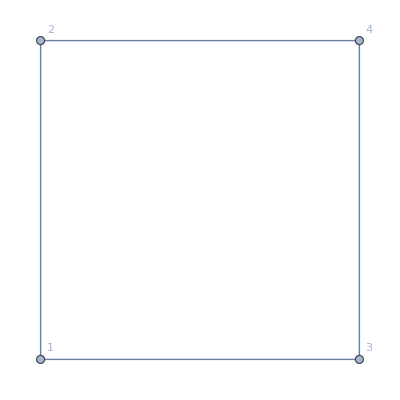

{-2,2,0,0}

```mathematica
(*2d Hypercube*)
G=HypercubeGraph[2,VertexLabels->"Name"]
Eigenvalues[MyAdjacencyMatrix[G]]
```

```mathematica
(*Eigenvalue 2*)
Simplify[Smash[G,{1,3,4}]]
Eigenvalues[Simplify[Smash[G, {1,3,4}]]]
mat = Simplify[Smash[G,{1,3,4}]] /. L -> Sqrt[15/2]
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> Sqrt[15/2]π]
```

{{1/L,1,1/L},{1,0,1},{1/L,1,1/L}}

{0,(1-√(1+2 L^2))/L,(1+√(1+2 L^2))/L}

{{√(2/15),1,√(2/15)},{1,0,1},{√(2/15),1,√(2/15)}}

{{1/16 (8+3 ⅇ^(-ⅈ √(6/5) t)+5 ⅇ^(ⅈ √(10/3) t)),1/8 √(15/2) ⅇ^(-ⅈ √(6/5) t) (-1+ⅇ^(8 ⅈ √(2/15) t)),1/16 (-8+3 ⅇ^(-ⅈ √(6/5) t)+5 ⅇ^(ⅈ √(10/3) t))},{1/8 √(15/2) ⅇ^(-ⅈ √(6/5) t) (-1+ⅇ^(8 ⅈ √(2/15) t)),1/8 ⅇ^(-ⅈ √(6/5) t) (5+3 ⅇ^(8 ⅈ √(2/15) t)),1/8 √(15/2) ⅇ^(-ⅈ √(6/5) t) (-1+ⅇ^(8 ⅈ √(2/15) t))},{1/16 (-8+3 ⅇ^(-ⅈ √(6/5) t)+5 ⅇ^(ⅈ √(10/3) t)),1/8 √(15/2) ⅇ^(-ⅈ √(6/5) t) (-1+ⅇ^(8 ⅈ √(2/15) t)),1/16 (8+3 ⅇ^(-ⅈ √(6/5) t)+5 ⅇ^(ⅈ √(10/3) t))}}

{{0,0,-1},{0,-1,0},{-1,0,0}}

```mathematica
(*Eigenvalue -1*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> -1
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{1,0,0,-2},{0,-1,0,0},{0,0,-1,0},{-2,0,0,1}}

{{ⅇ^(-ⅈ t)/2+1/2 ⅇ^(3 ⅈ t),0,0,ⅇ^(-ⅈ t)/2-1/2 ⅇ^(3 ⅈ t)},{0,ⅇ^(-ⅈ t),0,0},{0,0,ⅇ^(-ⅈ t),0},{ⅇ^(-ⅈ t)/2-1/2 ⅇ^(3 ⅈ t),0,0,ⅇ^(-ⅈ t)/2+1/2 ⅇ^(3 ⅈ t)}}

{{0,0,0,-(-1)^(3/4)},{0,-(-1)^(3/4),0,0},{0,0,-(-1)^(3/4),0},{-(-1)^(3/4),0,0,0}}

```mathematica
(*Eigenvalue 3*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> 3
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{51/55,64/55,24/55,26/55},{64/55,21/55,56/55,24/55},{24/55,56/55,21/55,64/55},{26/55,24/55,64/55,51/55}}

{{1/20 ⅇ^(-ⅈ t) (2+5 ⅇ^((4 ⅈ t)/5)+8 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (-4-5 ⅇ^((4 ⅈ t)/5)+4 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (4-5 ⅇ^((4 ⅈ t)/5)-4 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (-2+5 ⅇ^((4 ⅈ t)/5)-8 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t))},{1/20 ⅇ^(-ⅈ t) (-4-5 ⅇ^((4 ⅈ t)/5)+4 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (8+5 ⅇ^((4 ⅈ t)/5)+2 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (-8+5 ⅇ^((4 ⅈ t)/5)-2 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (4-5 ⅇ^((4 ⅈ t)/5)-4 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t))},{1/20 ⅇ^(-ⅈ t) (4-5 ⅇ^((4 ⅈ t)/5)-4 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (-8+5 ⅇ^((4 ⅈ t)/5)-2 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (8+5 ⅇ^((4 ⅈ t)/5)+2 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (-4-5 ⅇ^((4 ⅈ t)/5)+4 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t))},{1/20 ⅇ^(-ⅈ t) (-2+5 ⅇ^((4 ⅈ t)/5)-8 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (4-5 ⅇ^((4 ⅈ t)/5)-4 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (-4-5 ⅇ^((4 ⅈ t)/5)+4 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-ⅈ t) (2+5 ⅇ^((4 ⅈ t)/5)+8 ⅇ^((20 ⅈ t)/11)+5 ⅇ^(4 ⅈ t))}}

{{-1/20 (-1)^(3/4) (-3+5 (-1)^(1/5)+8 (-1)^(5/11)),1/20 (-1)^(3/4) (9+5 (-1)^(1/5)-4 (-1)^(5/11)),1/20 (-1)^(3/4) (1+5 (-1)^(1/5)+4 (-1)^(5/11)),1/20 (-1)^(3/4) (7-5 (-1)^(1/5)+8 (-1)^(5/11))},{1/20 (-1)^(3/4) (9+5 (-1)^(1/5)-4 (-1)^(5/11)),-1/20 (-1)^(3/4) (3+5 (-1)^(1/5)+2 (-1)^(5/11)),1/20 (-1)^(3/4) (13-5 (-1)^(1/5)+2 (-1)^(5/11)),1/20 (-1)^(3/4) (1+5 (-1)^(1/5)+4 (-1)^(5/11))},{1/20 (-1)^(3/4) (1+5 (-1)^(1/5)+4 (-1)^(5/11)),1/20 (-1)^(3/4) (13-5 (-1)^(1/5)+2 (-1)^(5/11)),-1/20 (-1)^(3/4) (3+5 (-1)^(1/5)+2 (-1)^(5/11)),1/20 (-1)^(3/4) (9+5 (-1)^(1/5)-4 (-1)^(5/11))},{1/20 (-1)^(3/4) (7-5 (-1)^(1/5)+8 (-1)^(5/11)),1/20 (-1)^(3/4) (1+5 (-1)^(1/5)+4 (-1)^(5/11)),1/20 (-1)^(3/4) (9+5 (-1)^(1/5)-4 (-1)^(5/11)),-1/20 (-1)^(3/4) (-3+5 (-1)^(1/5)+8 (-1)^(5/11))}}

```mathematica
(*Eigenvalue -3*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> -3
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{-51/55,64/55,-24/55,26/55},{64/55,-21/55,56/55,-24/55},{-24/55,56/55,-21/55,64/55},{26/55,-24/55,64/55,-51/55}}

{{1/20 ⅇ^(-3 ⅈ t) (5+8 ⅇ^((24 ⅈ t)/11)+5 ⅇ^((16 ⅈ t)/5)+2 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (-5-4 ⅇ^((24 ⅈ t)/11)+5 ⅇ^((16 ⅈ t)/5)+4 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (5-4 ⅇ^((24 ⅈ t)/11)-5 ⅇ^((16 ⅈ t)/5)+4 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (-5+8 ⅇ^((24 ⅈ t)/11)-5 ⅇ^((16 ⅈ t)/5)+2 ⅇ^(4 ⅈ t))},{1/20 ⅇ^(-3 ⅈ t) (-5-4 ⅇ^((24 ⅈ t)/11)+5 ⅇ^((16 ⅈ t)/5)+4 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (5+2 ⅇ^((24 ⅈ t)/11)+5 ⅇ^((16 ⅈ t)/5)+8 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (-5+2 ⅇ^((24 ⅈ t)/11)-5 ⅇ^((16 ⅈ t)/5)+8 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (5-4 ⅇ^((24 ⅈ t)/11)-5 ⅇ^((16 ⅈ t)/5)+4 ⅇ^(4 ⅈ t))},{1/20 ⅇ^(-3 ⅈ t) (5-4 ⅇ^((24 ⅈ t)/11)-5 ⅇ^((16 ⅈ t)/5)+4 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (-5+2 ⅇ^((24 ⅈ t)/11)-5 ⅇ^((16 ⅈ t)/5)+8 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (5+2 ⅇ^((24 ⅈ t)/11)+5 ⅇ^((16 ⅈ t)/5)+8 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (-5-4 ⅇ^((24 ⅈ t)/11)+5 ⅇ^((16 ⅈ t)/5)+4 ⅇ^(4 ⅈ t))},{1/20 ⅇ^(-3 ⅈ t) (-5+8 ⅇ^((24 ⅈ t)/11)-5 ⅇ^((16 ⅈ t)/5)+2 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (5-4 ⅇ^((24 ⅈ t)/11)-5 ⅇ^((16 ⅈ t)/5)+4 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (-5-4 ⅇ^((24 ⅈ t)/11)+5 ⅇ^((16 ⅈ t)/5)+4 ⅇ^(4 ⅈ t)),1/20 ⅇ^(-3 ⅈ t) (5+8 ⅇ^((24 ⅈ t)/11)+5 ⅇ^((16 ⅈ t)/5)+2 ⅇ^(4 ⅈ t))}}

{{-1/20 (-1)^(1/4) (3+8 (-1)^(6/11)+5 (-1)^(4/5)),1/20 (-1)^(1/4) (9+4 (-1)^(6/11)-5 (-1)^(4/5)),1/20 (-1)^(1/4) (-1+4 (-1)^(6/11)+5 (-1)^(4/5)),1/20 (-1)^(1/4) (7-8 (-1)^(6/11)+5 (-1)^(4/5))},{1/20 (-1)^(1/4) (9+4 (-1)^(6/11)-5 (-1)^(4/5)),-1/20 (-1)^(1/4) (-3+2 (-1)^(6/11)+5 (-1)^(4/5)),1/20 (-1)^(1/4) (13-2 (-1)^(6/11)+5 (-1)^(4/5)),1/20 (-1)^(1/4) (-1+4 (-1)^(6/11)+5 (-1)^(4/5))},{1/20 (-1)^(1/4) (-1+4 (-1)^(6/11)+5 (-1)^(4/5)),1/20 (-1)^(1/4) (13-2 (-1)^(6/11)+5 (-1)^(4/5)),-1/20 (-1)^(1/4) (-3+2 (-1)^(6/11)+5 (-1)^(4/5)),1/20 (-1)^(1/4) (9+4 (-1)^(6/11)-5 (-1)^(4/5))},{1/20 (-1)^(1/4) (7-8 (-1)^(6/11)+5 (-1)^(4/5)),1/20 (-1)^(1/4) (-1+4 (-1)^(6/11)+5 (-1)^(4/5)),1/20 (-1)^(1/4) (9+4 (-1)^(6/11)-5 (-1)^(4/5)),-1/20 (-1)^(1/4) (3+8 (-1)^(6/11)+5 (-1)^(4/5))}}

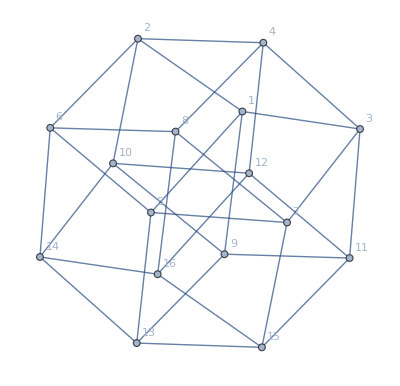

{-4,4,-2,-2,-2,-2,2,2,2,2,0,0,0,0,0,0}

```mathematica
(*4d Hypercube*)
G=HypercubeGraph[4,VertexLabels->"Name"]
Eigenvalues[MyAdjacencyMatrix[G]]
```

```mathematica
(*Eigenvalue 2*) 
Simplify[Smash[G,{2,1,5,7,15}]]
mat = Simplify[Smash[G,{2,1,5,7,15}]] /. L -> 2
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/3]
```

{{(64-180 L^2+128 L^4-34 L^6+3 L^8)/(48 L-124 L^3+75 L^5-16 L^7+L^9),(32-104 L^2+64 L^4-14 L^6+L^8)/(48-124 L^2+75 L^4-16 L^6+L^8),(L (8-6 L^2+L^4))/(-16+36 L^2-13 L^4+L^6),(-32+56 L^2-24 L^4+3 L^6)/(48-124 L^2+75 L^4-16 L^6+L^8),-(64-156 L^2+84 L^4-13 L^6)/(48 L-124 L^3+75 L^5-16 L^7+L^9)},{(32-104 L^2+64 L^4-14 L^6+L^8)/(48-124 L^2+75 L^4-16 L^6+L^8),(L (-80+84 L^2-25 L^4+2 L^6))/(48-124 L^2+75 L^4-16 L^6+L^8),(L^2 (32-12 L^2+L^4))/(-16+36 L^2-13 L^4+L^6),(L (-4+L^2)^3)/(48-124 L^2+75 L^4-16 L^6+L^8),(-32+56 L^2-24 L^4+3 L^6)/(48-124 L^2+75 L^4-16 L^6+L^8)},{(L (8-6 L^2+L^4))/(-16+36 L^2-13 L^4+L^6),(L^2 (32-12 L^2+L^4))/(-16+36 L^2-13 L^4+L^6),(2 L (16-10 L^2+L^4))/(-16+36 L^2-13 L^4+L^6),(L^2 (32-12 L^2+L^4))/(-16+36 L^2-13 L^4+L^6),(L (8-6 L^2+L^4))/(-16+36 L^2-13 L^4+L^6)},{(-32+56 L^2-24 L^4+3 L^6)/(48-124 L^2+75 L^4-16 L^6+L^8),(L (-4+L^2)^3)/(48-124 L^2+75 L^4-16 L^6+L^8),(L^2 (32-12 L^2+L^4))/(-16+36 L^2-13 L^4+L^6),(L (-80+84 L^2-25 L^4+2 L^6))/(48-124 L^2+75 L^4-16 L^6+L^8),(32-104 L^2+64 L^4-14 L^6+L^8)/(48-124 L^2+75 L^4-16 L^6+L^8)},{-(64-156 L^2+84 L^4-13 L^6)/(48 L-124 L^3+75 L^5-16 L^7+L^9),(-32+56 L^2-24 L^4+3 L^6)/(48-124 L^2+75 L^4-16 L^6+L^8),(L (8-6 L^2+L^4))/(-16+36 L^2-13 L^4+L^6),(32-104 L^2+64 L^4-14 L^6+L^8)/(48-124 L^2+75 L^4-16 L^6+L^8),(64-180 L^2+128 L^4-34 L^6+3 L^8)/(48 L-124 L^3+75 L^5-16 L^7+L^9)}}

{{1/2,0,0,0,-3/2},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{-3/2,0,0,0,1/2}}

{{1/2 ⅇ^(-ⅈ t) (1+ⅇ^(3 ⅈ t)),0,0,0,-1/2 ⅇ^(-ⅈ t) (-1+ⅇ^(3 ⅈ t))},{0,ⅇ^(2 ⅈ t),0,0,0},{0,0,ⅇ^(2 ⅈ t),0,0},{0,0,0,ⅇ^(2 ⅈ t),0},{-1/2 ⅇ^(-ⅈ t) (-1+ⅇ^(3 ⅈ t)),0,0,0,1/2 ⅇ^(-ⅈ t) (1+ⅇ^(3 ⅈ t))}}

{{0,0,0,0,-(-1)^(2/3)},{0,(-1)^(2/3),0,0,0},{0,0,(-1)^(2/3),0,0},{0,0,0,(-1)^(2/3),0},{-(-1)^(2/3),0,0,0,0}}

```mathematica
(*Eigenvalue -2*)
mat = Simplify[Smash[G,{2,1,5,7,15}]] /. L -> -2
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/3]
```

{{-1/2,0,0,0,3/2},{0,-2,0,0,0},{0,0,-2,0,0},{0,0,0,-2,0},{3/2,0,0,0,-1/2}}

{{1/2 ⅇ^(-2 ⅈ t) (1+ⅇ^(3 ⅈ t)),0,0,0,1/2 ⅇ^(-2 ⅈ t) (-1+ⅇ^(3 ⅈ t))},{0,ⅇ^(-2 ⅈ t),0,0,0},{0,0,ⅇ^(-2 ⅈ t),0,0},{0,0,0,ⅇ^(-2 ⅈ t),0},{1/2 ⅇ^(-2 ⅈ t) (-1+ⅇ^(3 ⅈ t)),0,0,0,1/2 ⅇ^(-2 ⅈ t) (1+ⅇ^(3 ⅈ t))}}

{{0,0,0,0,(-1)^(1/3)},{0,-(-1)^(1/3),0,0,0},{0,0,-(-1)^(1/3),0,0},{0,0,0,-(-1)^(1/3),0},{(-1)^(1/3),0,0,0,0}}

```mathematica
(*Eigenvalue -4*)
mat = Simplify[Smash[G,{2,1,5,7,15}]] /. L -> -4
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/3]
```

{{-1364/1079,1434/1079,-42/83,438/1079,-534/1079},{1434/1079,-764/1079,96/83,-432/1079,438/1079},{-42/83,96/83,-56/83,96/83,-42/83},{438/1079,-432/1079,96/83,-764/1079,1434/1079},{-534/1079,438/1079,-42/83,1434/1079,-1364/1079}}

{{1/139060 ⅇ^(-(ⅈ (4316+249 √17+39 √409) t)/1079) (17 (1227+41 √409) ⅇ^((3 ⅈ (1521+83 √17) t)/1079)-2045 (-17+√17) ⅇ^((3 ⅈ (1245+166 √17+13 √409) t)/1079)+(20859-697 √409) ⅇ^((3 ⅈ (1521+83 √17+26 √409) t)/1079)+2045 (17+√17) ⅇ^((45 ⅈ t)/13+3/83 ⅈ √409 t)+27812 ⅇ^(3/13 ⅈ √17 t+3/83 ⅈ √409 t)),-1/5 ⅇ^(-4 ⅈ t)+ⅇ^(1/13 ⅈ (-7+3 √17) t)/(√17)-ⅇ^(-1/13 ⅈ (7+3 √17) t)/(√17)+(1/10-3/(10 √409)) ⅇ^(-1/83 ⅈ (-19+3 √409) t)+(1/10+3/(10 √409)) ⅇ^(1/83 ⅈ (19+3 √409) t),(ⅇ^(-1/83 ⅈ (332+3 √409) t) (-((409+47 √409) ⅇ^((351 ⅈ t)/83))+818 ⅇ^(3/83 ⅈ √409 t)+(-409+47 √409) ⅇ^(3/83 ⅈ (117+2 √409) t)))/4090,-1/5 ⅇ^(-4 ⅈ t)-ⅇ^(1/13 ⅈ (-7+3 √17) t)/(√17)+ⅇ^(-1/13 ⅈ (7+3 √17) t)/(√17)+(1/10-3/(10 √409)) ⅇ^(-1/83 ⅈ (-19+3 √409) t)+(1/10+3/(10 √409)) ⅇ^(1/83 ⅈ (19+3 √409) t),1/139060 ⅇ^(-(ⅈ (4316+249 √17+39 √409) t)/1079) (17 (1227+41 √409) ⅇ^((3 ⅈ (1521+83 √17) t)/1079)+2045 (-17+√17) ⅇ^((3 ⅈ (1245+166 √17+13 √409) t)/1079)+(20859-697 √409) ⅇ^((3 ⅈ (1521+83 √17+26 √409) t)/1079)-2045 (17+√17) ⅇ^((45 ⅈ t)/13+3/83 ⅈ √409 t)+27812 ⅇ^(3/13 ⅈ √17 t+3/83 ⅈ √409 t))},{-1/5 ⅇ^(-4 ⅈ t)+ⅇ^(1/13 ⅈ (-7+3 √17) t)/(√17)-ⅇ^(-1/13 ⅈ (7+3 √17) t)/(√17)+(1/10-3/(10 √409)) ⅇ^(-1/83 ⅈ (-19+3 √409) t)+(1/10+3/(10 √409)) ⅇ^(1/83 ⅈ (19+3 √409) t),1/139060 ⅇ^(-(ⅈ (4316+249 √17+39 √409) t)/1079) ((20859-833 √409) ⅇ^((3 ⅈ (1521+83 √17) t)/1079)+2045 (17+√17) ⅇ^((3 ⅈ (1245+166 √17+13 √409) t)/1079)+17 (1227+49 √409) ⅇ^((3 ⅈ (1521+83 √17+26 √409) t)/1079)-2045 (-17+√17) ⅇ^((45 ⅈ t)/13+3/83 ⅈ √409 t)+27812 ⅇ^(3/13 ⅈ √17 t+3/83 ⅈ √409 t)),(ⅇ^(-1/83 ⅈ (332+3 √409) t) ((409-43 √409) ⅇ^((351 ⅈ t)/83)-818 ⅇ^(3/83 ⅈ √409 t)+(409+43 √409) ⅇ^(3/83 ⅈ (117+2 √409) t)))/4090,1/139060 ⅇ^(-(ⅈ (4316+249 √17+39 √409) t)/1079) ((20859-833 √409) ⅇ^((3 ⅈ (1521+83 √17) t)/1079)-2045 (17+√17) ⅇ^((3 ⅈ (1245+166 √17+13 √409) t)/1079)+17 (1227+49 √409) ⅇ^((3 ⅈ (1521+83 √17+26 √409) t)/1079)+2045 (-17+√17) ⅇ^((45 ⅈ t)/13+3/83 ⅈ √409 t)+27812 ⅇ^(3/13 ⅈ √17 t+3/83 ⅈ √409 t)),-1/5 ⅇ^(-4 ⅈ t)-ⅇ^(1/13 ⅈ (-7+3 √17) t)/(√17)+ⅇ^(-1/13 ⅈ (7+3 √17) t)/(√17)+(1/10-3/(10 √409)) ⅇ^(-1/83 ⅈ (-19+3 √409) t)+(1/10+3/(10 √409)) ⅇ^(1/83 ⅈ (19+3 √409) t)},{(ⅇ^(-1/83 ⅈ (332+3 √409) t) (-((409+47 √409) ⅇ^((351 ⅈ t)/83))+818 ⅇ^(3/83 ⅈ √409 t)+(-409+47 √409) ⅇ^(3/83 ⅈ (117+2 √409) t)))/4090,(ⅇ^(-1/83 ⅈ (332+3 √409) t) ((409-43 √409) ⅇ^((351 ⅈ t)/83)-818 ⅇ^(3/83 ⅈ √409 t)+(409+43 √409) ⅇ^(3/83 ⅈ (117+2 √409) t)))/4090,(ⅇ^(-1/83 ⅈ (332+3 √409) t) ((818+4 √409) ⅇ^((351 ⅈ t)/83)+409 ⅇ^(3/83 ⅈ √409 t)+(818-4 √409) ⅇ^(3/83 ⅈ (117+2 √409) t)))/2045,(ⅇ^(-1/83 ⅈ (332+3 √409) t) ((409-43 √409) ⅇ^((351 ⅈ t)/83)-818 ⅇ^(3/83 ⅈ √409 t)+(409+43 √409) ⅇ^(3/83 ⅈ (117+2 √409) t)))/4090,(ⅇ^(-1/83 ⅈ (332+3 √409) t) (-((409+47 √409) ⅇ^((351 ⅈ t)/83))+818 ⅇ^(3/83 ⅈ √409 t)+(-409+47 √409) ⅇ^(3/83 ⅈ (117+2 √409) t)))/4090},{-1/5 ⅇ^(-4 ⅈ t)-ⅇ^(1/13 ⅈ (-7+3 √17) t)/(√17)+ⅇ^(-1/13 ⅈ (7+3 √17) t)/(√17)+(1/10-3/(10 √409)) ⅇ^(-1/83 ⅈ (-19+3 √409) t)+(1/10+3/(10 √409)) ⅇ^(1/83 ⅈ (19+3 √409) t),1/139060 ⅇ^(-(ⅈ (4316+249 √17+39 √409) t)/1079) ((20859-833 √409) ⅇ^((3 ⅈ (1521+83 √17) t)/1079)-2045 (17+√17) ⅇ^((3 ⅈ (1245+166 √17+13 √409) t)/1079)+17 (1227+49 √409) ⅇ^((3 ⅈ (1521+83 √17+26 √409) t)/1079)+2045 (-17+√17) ⅇ^((45 ⅈ t)/13+3/83 ⅈ √409 t)+27812 ⅇ^(3/13 ⅈ √17 t+3/83 ⅈ √409 t)),(ⅇ^(-1/83 ⅈ (332+3 √409) t) ((409-43 √409) ⅇ^((351 ⅈ t)/83)-818 ⅇ^(3/83 ⅈ √409 t)+(409+43 √409) ⅇ^(3/83 ⅈ (117+2 √409) t)))/4090,1/139060 ⅇ^(-(ⅈ (4316+249 √17+39 √409) t)/1079) ((20859-833 √409) ⅇ^((3 ⅈ (1521+83 √17) t)/1079)+2045 (17+√17) ⅇ^((3 ⅈ (1245+166 √17+13 √409) t)/1079)+17 (1227+49 √409) ⅇ^((3 ⅈ (1521+83 √17+26 √409) t)/1079)-2045 (-17+√17) ⅇ^((45 ⅈ t)/13+3/83 ⅈ √409 t)+27812 ⅇ^(3/13 ⅈ √17 t+3/83 ⅈ √409 t)),-1/5 ⅇ^(-4 ⅈ t)+ⅇ^(1/13 ⅈ (-7+3 √17) t)/(√17)-ⅇ^(-1/13 ⅈ (7+3 √17) t)/(√17)+(1/10-3/(10 √409)) ⅇ^(-1/83 ⅈ (-19+3 √409) t)+(1/10+3/(10 √409)) ⅇ^(1/83 ⅈ (19+3 √409) t)},{1/139060 ⅇ^(-(ⅈ (4316+249 √17+39 √409) t)/1079) (17 (1227+41 √409) ⅇ^((3 ⅈ (1521+83 √17) t)/1079)+2045 (-17+√17) ⅇ^((3 ⅈ (1245+166 √17+13 √409) t)/1079)+(20859-697 √409) ⅇ^((3 ⅈ (1521+83 √17+26 √409) t)/1079)-2045 (17+√17) ⅇ^((45 ⅈ t)/13+3/83 ⅈ √409 t)+27812 ⅇ^(3/13 ⅈ √17 t+3/83 ⅈ √409 t)),-1/5 ⅇ^(-4 ⅈ t)-ⅇ^(1/13 ⅈ (-7+3 √17) t)/(√17)+ⅇ^(-1/13 ⅈ (7+3 √17) t)/(√17)+(1/10-3/(10 √409)) ⅇ^(-1/83 ⅈ (-19+3 √409) t)+(1/10+3/(10 √409)) ⅇ^(1/83 ⅈ (19+3 √409) t),(ⅇ^(-1/83 ⅈ (332+3 √409) t) (-((409+47 √409) ⅇ^((351 ⅈ t)/83))+818 ⅇ^(3/83 ⅈ √409 t)+(-409+47 √409) ⅇ^(3/83 ⅈ (117+2 √409) t)))/4090,-1/5 ⅇ^(-4 ⅈ t)+ⅇ^(1/13 ⅈ (-7+3 √17) t)/(√17)-ⅇ^(-1/13 ⅈ (7+3 √17) t)/(√17)+(1/10-3/(10 √409)) ⅇ^(-1/83 ⅈ (-19+3 √409) t)+(1/10+3/(10 √409)) ⅇ^(1/83 ⅈ (19+3 √409) t),1/139060 ⅇ^(-(ⅈ (4316+249 √17+39 √409) t)/1079) (17 (1227+41 √409) ⅇ^((3 ⅈ (1521+83 √17) t)/1079)-2045 (-17+√17) ⅇ^((3 ⅈ (1245+166 √17+13 √409) t)/1079)+(20859-697 √409) ⅇ^((3 ⅈ (1521+83 √17+26 √409) t)/1079)+2045 (17+√17) ⅇ^((45 ⅈ t)/13+3/83 ⅈ √409 t)+27812 ⅇ^(3/13 ⅈ √17 t+3/83 ⅈ √409 t))}}

{{1/5 (-1)^(2/3)-1/68 (-1)^(32/39) (17+√17) ⅇ^(-1/13 ⅈ √17 π)+1/68 (-1)^(32/39) (-17+√17) ⅇ^(1/13 ⅈ √17 π)+((-1)^(19/249) (1227+41 √409) ⅇ^(-1/83 ⅈ √409 π))/8180+((-1)^(19/249) (1227-41 √409) ⅇ^(1/83 ⅈ √409 π))/8180,-1/5 (-1)^(2/3)+((-1)^(32/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)-((-1)^(32/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(19/249) (409-3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(19/249) (409+3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,((-1)^(19/249) ⅇ^(-1/83 ⅈ √409 π) (-409-47 √409+818 (-1)^(49/83) ⅇ^(1/83 ⅈ √409 π)+(-409+47 √409) ⅇ^(2/83 ⅈ √409 π)))/4090,-1/5 (-1)^(2/3)-((-1)^(32/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)+((-1)^(32/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(19/249) (409-3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(19/249) (409+3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,1/5 (-1)^(2/3)+1/68 (-1)^(32/39) (17+√17) ⅇ^(-1/13 ⅈ √17 π)-1/68 (-1)^(32/39) (-17+√17) ⅇ^(1/13 ⅈ √17 π)+((-1)^(19/249) (1227+41 √409) ⅇ^(-1/83 ⅈ √409 π))/8180+((-1)^(19/249) (1227-41 √409) ⅇ^(1/83 ⅈ √409 π))/8180},{-1/5 (-1)^(2/3)+((-1)^(32/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)-((-1)^(32/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(19/249) (409-3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(19/249) (409+3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,1/5 (-1)^(2/3)+1/68 (-1)^(32/39) (-17+√17) ⅇ^(-1/13 ⅈ √17 π)-1/68 (-1)^(32/39) (17+√17) ⅇ^(1/13 ⅈ √17 π)+((-1)^(19/249) (1227-49 √409) ⅇ^(-1/83 ⅈ √409 π))/8180+((-1)^(19/249) (1227+49 √409) ⅇ^(1/83 ⅈ √409 π))/8180,((-1)^(19/249) ⅇ^(-1/83 ⅈ √409 π) (409-43 √409-818 (-1)^(49/83) ⅇ^(1/83 ⅈ √409 π)+(409+43 √409) ⅇ^(2/83 ⅈ √409 π)))/4090,1/5 (-1)^(2/3)-1/68 (-1)^(32/39) (-17+√17) ⅇ^(-1/13 ⅈ √17 π)+1/68 (-1)^(32/39) (17+√17) ⅇ^(1/13 ⅈ √17 π)+((-1)^(19/249) (1227-49 √409) ⅇ^(-1/83 ⅈ √409 π))/8180+((-1)^(19/249) (1227+49 √409) ⅇ^(1/83 ⅈ √409 π))/8180,-1/5 (-1)^(2/3)-((-1)^(32/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)+((-1)^(32/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(19/249) (409-3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(19/249) (409+3 √409) ⅇ^(1/83 ⅈ √409 π))/4090},{((-1)^(19/249) ⅇ^(-1/83 ⅈ √409 π) (-409-47 √409+818 (-1)^(49/83) ⅇ^(1/83 ⅈ √409 π)+(-409+47 √409) ⅇ^(2/83 ⅈ √409 π)))/4090,((-1)^(19/249) ⅇ^(-1/83 ⅈ √409 π) (409-43 √409-818 (-1)^(49/83) ⅇ^(1/83 ⅈ √409 π)+(409+43 √409) ⅇ^(2/83 ⅈ √409 π)))/4090,((-1)^(19/249) ⅇ^(-1/83 ⅈ √409 π) (818+4 √409+409 (-1)^(49/83) ⅇ^(1/83 ⅈ √409 π)+(818-4 √409) ⅇ^(2/83 ⅈ √409 π)))/2045,((-1)^(19/249) ⅇ^(-1/83 ⅈ √409 π) (409-43 √409-818 (-1)^(49/83) ⅇ^(1/83 ⅈ √409 π)+(409+43 √409) ⅇ^(2/83 ⅈ √409 π)))/4090,((-1)^(19/249) ⅇ^(-1/83 ⅈ √409 π) (-409-47 √409+818 (-1)^(49/83) ⅇ^(1/83 ⅈ √409 π)+(-409+47 √409) ⅇ^(2/83 ⅈ √409 π)))/4090},{-1/5 (-1)^(2/3)-((-1)^(32/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)+((-1)^(32/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(19/249) (409-3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(19/249) (409+3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,1/5 (-1)^(2/3)-1/68 (-1)^(32/39) (-17+√17) ⅇ^(-1/13 ⅈ √17 π)+1/68 (-1)^(32/39) (17+√17) ⅇ^(1/13 ⅈ √17 π)+((-1)^(19/249) (1227-49 √409) ⅇ^(-1/83 ⅈ √409 π))/8180+((-1)^(19/249) (1227+49 √409) ⅇ^(1/83 ⅈ √409 π))/8180,((-1)^(19/249) ⅇ^(-1/83 ⅈ √409 π) (409-43 √409-818 (-1)^(49/83) ⅇ^(1/83 ⅈ √409 π)+(409+43 √409) ⅇ^(2/83 ⅈ √409 π)))/4090,1/5 (-1)^(2/3)+1/68 (-1)^(32/39) (-17+√17) ⅇ^(-1/13 ⅈ √17 π)-1/68 (-1)^(32/39) (17+√17) ⅇ^(1/13 ⅈ √17 π)+((-1)^(19/249) (1227-49 √409) ⅇ^(-1/83 ⅈ √409 π))/8180+((-1)^(19/249) (1227+49 √409) ⅇ^(1/83 ⅈ √409 π))/8180,-1/5 (-1)^(2/3)+((-1)^(32/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)-((-1)^(32/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(19/249) (409-3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(19/249) (409+3 √409) ⅇ^(1/83 ⅈ √409 π))/4090},{1/5 (-1)^(2/3)+1/68 (-1)^(32/39) (17+√17) ⅇ^(-1/13 ⅈ √17 π)-1/68 (-1)^(32/39) (-17+√17) ⅇ^(1/13 ⅈ √17 π)+((-1)^(19/249) (1227+41 √409) ⅇ^(-1/83 ⅈ √409 π))/8180+((-1)^(19/249) (1227-41 √409) ⅇ^(1/83 ⅈ √409 π))/8180,-1/5 (-1)^(2/3)-((-1)^(32/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)+((-1)^(32/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(19/249) (409-3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(19/249) (409+3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,((-1)^(19/249) ⅇ^(-1/83 ⅈ √409 π) (-409-47 √409+818 (-1)^(49/83) ⅇ^(1/83 ⅈ √409 π)+(-409+47 √409) ⅇ^(2/83 ⅈ √409 π)))/4090,-1/5 (-1)^(2/3)+((-1)^(32/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)-((-1)^(32/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(19/249) (409-3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(19/249) (409+3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,1/5 (-1)^(2/3)-1/68 (-1)^(32/39) (17+√17) ⅇ^(-1/13 ⅈ √17 π)+1/68 (-1)^(32/39) (-17+√17) ⅇ^(1/13 ⅈ √17 π)+((-1)^(19/249) (1227+41 √409) ⅇ^(-1/83 ⅈ √409 π))/8180+((-1)^(19/249) (1227-41 √409) ⅇ^(1/83 ⅈ √409 π))/8180}}

```mathematica
(*Eigenvalue -4*)
mat = Simplify[Smash[G,{2,1,5,7,15}]] /. L -> 4
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/3]
```

{{1364/1079,1434/1079,42/83,438/1079,534/1079},{1434/1079,764/1079,96/83,432/1079,438/1079},{42/83,96/83,56/83,96/83,42/83},{438/1079,432/1079,96/83,764/1079,1434/1079},{534/1079,438/1079,42/83,1434/1079,1364/1079}}

{{1/139060 ⅇ^(-(ⅈ (247+249 √17+39 √409) t)/1079) ((20859-697 √409) ⅇ^(3/13 ⅈ √17 t)-2045 (-17+√17) ⅇ^((3 ⅈ (276+13 √409) t)/1079)+27812 ⅇ^((3 ⅈ (1521+83 √17+13 √409) t)/1079)+2045 (17+√17) ⅇ^((3 ⅈ (276+166 √17+13 √409) t)/1079)+17 (1227+41 √409) ⅇ^(3/13 ⅈ √17 t+6/83 ⅈ √409 t)),1/69530 ⅇ^(-(19 ⅈ t)/83) (13906 ⅇ^((351 ⅈ t)/83)-17 (409+3 √409) ⅇ^(-3/83 ⅈ √409 t)+17 (-409+3 √409) ⅇ^(3/83 ⅈ √409 t)-4090 √17 ⅇ^(-(3 ⅈ (-276+83 √17) t)/1079)+4090 √17 ⅇ^((3 ⅈ (276+83 √17) t)/1079)),-(ⅇ^(-1/83 ⅈ (19+3 √409) t) (409-47 √409+(409+47 √409) ⅇ^(6/83 ⅈ √409 t)-818 ⅇ^(3/83 ⅈ (117+√409) t)))/4090,1/69530 ⅇ^(-(19 ⅈ t)/83) (13906 ⅇ^((351 ⅈ t)/83)-17 (409+3 √409) ⅇ^(-3/83 ⅈ √409 t)+17 (-409+3 √409) ⅇ^(3/83 ⅈ √409 t)+4090 √17 ⅇ^(-(3 ⅈ (-276+83 √17) t)/1079)-4090 √17 ⅇ^((3 ⅈ (276+83 √17) t)/1079)),1/139060 ⅇ^(-(ⅈ (247+249 √17+39 √409) t)/1079) ((20859-697 √409) ⅇ^(3/13 ⅈ √17 t)+2045 (-17+√17) ⅇ^((3 ⅈ (276+13 √409) t)/1079)+27812 ⅇ^((3 ⅈ (1521+83 √17+13 √409) t)/1079)-2045 (17+√17) ⅇ^((3 ⅈ (276+166 √17+13 √409) t)/1079)+17 (1227+41 √409) ⅇ^(3/13 ⅈ √17 t+6/83 ⅈ √409 t))},{1/69530 ⅇ^(-(19 ⅈ t)/83) (13906 ⅇ^((351 ⅈ t)/83)-17 (409+3 √409) ⅇ^(-3/83 ⅈ √409 t)+17 (-409+3 √409) ⅇ^(3/83 ⅈ √409 t)-4090 √17 ⅇ^(-(3 ⅈ (-276+83 √17) t)/1079)+4090 √17 ⅇ^((3 ⅈ (276+83 √17) t)/1079)),1/139060 ⅇ^(-(ⅈ (247+249 √17+39 √409) t)/1079) (17 (1227+49 √409) ⅇ^(3/13 ⅈ √17 t)+2045 (17+√17) ⅇ^((3 ⅈ (276+13 √409) t)/1079)+27812 ⅇ^((3 ⅈ (1521+83 √17+13 √409) t)/1079)-2045 (-17+√17) ⅇ^((3 ⅈ (276+166 √17+13 √409) t)/1079)+(20859-833 √409) ⅇ^(3/13 ⅈ √17 t+6/83 ⅈ √409 t)),(ⅇ^(-1/83 ⅈ (19+3 √409) t) (-409-43 √409+(-409+43 √409) ⅇ^(6/83 ⅈ √409 t)+818 ⅇ^(3/83 ⅈ (117+√409) t)))/4090,1/139060 ⅇ^(-(ⅈ (247+249 √17+39 √409) t)/1079) (17 (1227+49 √409) ⅇ^(3/13 ⅈ √17 t)-2045 (17+√17) ⅇ^((3 ⅈ (276+13 √409) t)/1079)+27812 ⅇ^((3 ⅈ (1521+83 √17+13 √409) t)/1079)+2045 (-17+√17) ⅇ^((3 ⅈ (276+166 √17+13 √409) t)/1079)+(20859-833 √409) ⅇ^(3/13 ⅈ √17 t+6/83 ⅈ √409 t)),1/69530 ⅇ^(-(19 ⅈ t)/83) (13906 ⅇ^((351 ⅈ t)/83)-17 (409+3 √409) ⅇ^(-3/83 ⅈ √409 t)+17 (-409+3 √409) ⅇ^(3/83 ⅈ √409 t)+4090 √17 ⅇ^(-(3 ⅈ (-276+83 √17) t)/1079)-4090 √17 ⅇ^((3 ⅈ (276+83 √17) t)/1079))},{-(ⅇ^(-1/83 ⅈ (19+3 √409) t) (409-47 √409+(409+47 √409) ⅇ^(6/83 ⅈ √409 t)-818 ⅇ^(3/83 ⅈ (117+√409) t)))/4090,(ⅇ^(-1/83 ⅈ (19+3 √409) t) (-409-43 √409+(-409+43 √409) ⅇ^(6/83 ⅈ √409 t)+818 ⅇ^(3/83 ⅈ (117+√409) t)))/4090,(ⅇ^(-1/83 ⅈ (19+3 √409) t) (818-4 √409+(818+4 √409) ⅇ^(6/83 ⅈ √409 t)+409 ⅇ^(3/83 ⅈ (117+√409) t)))/2045,(ⅇ^(-1/83 ⅈ (19+3 √409) t) (-409-43 √409+(-409+43 √409) ⅇ^(6/83 ⅈ √409 t)+818 ⅇ^(3/83 ⅈ (117+√409) t)))/4090,-(ⅇ^(-1/83 ⅈ (19+3 √409) t) (409-47 √409+(409+47 √409) ⅇ^(6/83 ⅈ √409 t)-818 ⅇ^(3/83 ⅈ (117+√409) t)))/4090},{1/69530 ⅇ^(-(19 ⅈ t)/83) (13906 ⅇ^((351 ⅈ t)/83)-17 (409+3 √409) ⅇ^(-3/83 ⅈ √409 t)+17 (-409+3 √409) ⅇ^(3/83 ⅈ √409 t)+4090 √17 ⅇ^(-(3 ⅈ (-276+83 √17) t)/1079)-4090 √17 ⅇ^((3 ⅈ (276+83 √17) t)/1079)),1/139060 ⅇ^(-(ⅈ (247+249 √17+39 √409) t)/1079) (17 (1227+49 √409) ⅇ^(3/13 ⅈ √17 t)-2045 (17+√17) ⅇ^((3 ⅈ (276+13 √409) t)/1079)+27812 ⅇ^((3 ⅈ (1521+83 √17+13 √409) t)/1079)+2045 (-17+√17) ⅇ^((3 ⅈ (276+166 √17+13 √409) t)/1079)+(20859-833 √409) ⅇ^(3/13 ⅈ √17 t+6/83 ⅈ √409 t)),(ⅇ^(-1/83 ⅈ (19+3 √409) t) (-409-43 √409+(-409+43 √409) ⅇ^(6/83 ⅈ √409 t)+818 ⅇ^(3/83 ⅈ (117+√409) t)))/4090,1/139060 ⅇ^(-(ⅈ (247+249 √17+39 √409) t)/1079) (17 (1227+49 √409) ⅇ^(3/13 ⅈ √17 t)+2045 (17+√17) ⅇ^((3 ⅈ (276+13 √409) t)/1079)+27812 ⅇ^((3 ⅈ (1521+83 √17+13 √409) t)/1079)-2045 (-17+√17) ⅇ^((3 ⅈ (276+166 √17+13 √409) t)/1079)+(20859-833 √409) ⅇ^(3/13 ⅈ √17 t+6/83 ⅈ √409 t)),1/69530 ⅇ^(-(19 ⅈ t)/83) (13906 ⅇ^((351 ⅈ t)/83)-17 (409+3 √409) ⅇ^(-3/83 ⅈ √409 t)+17 (-409+3 √409) ⅇ^(3/83 ⅈ √409 t)-4090 √17 ⅇ^(-(3 ⅈ (-276+83 √17) t)/1079)+4090 √17 ⅇ^((3 ⅈ (276+83 √17) t)/1079))},{1/139060 ⅇ^(-(ⅈ (247+249 √17+39 √409) t)/1079) ((20859-697 √409) ⅇ^(3/13 ⅈ √17 t)+2045 (-17+√17) ⅇ^((3 ⅈ (276+13 √409) t)/1079)+27812 ⅇ^((3 ⅈ (1521+83 √17+13 √409) t)/1079)-2045 (17+√17) ⅇ^((3 ⅈ (276+166 √17+13 √409) t)/1079)+17 (1227+41 √409) ⅇ^(3/13 ⅈ √17 t+6/83 ⅈ √409 t)),1/69530 ⅇ^(-(19 ⅈ t)/83) (13906 ⅇ^((351 ⅈ t)/83)-17 (409+3 √409) ⅇ^(-3/83 ⅈ √409 t)+17 (-409+3 √409) ⅇ^(3/83 ⅈ √409 t)+4090 √17 ⅇ^(-(3 ⅈ (-276+83 √17) t)/1079)-4090 √17 ⅇ^((3 ⅈ (276+83 √17) t)/1079)),-(ⅇ^(-1/83 ⅈ (19+3 √409) t) (409-47 √409+(409+47 √409) ⅇ^(6/83 ⅈ √409 t)-818 ⅇ^(3/83 ⅈ (117+√409) t)))/4090,1/69530 ⅇ^(-(19 ⅈ t)/83) (13906 ⅇ^((351 ⅈ t)/83)-17 (409+3 √409) ⅇ^(-3/83 ⅈ √409 t)+17 (-409+3 √409) ⅇ^(3/83 ⅈ √409 t)-4090 √17 ⅇ^(-(3 ⅈ (-276+83 √17) t)/1079)+4090 √17 ⅇ^((3 ⅈ (276+83 √17) t)/1079)),1/139060 ⅇ^(-(ⅈ (247+249 √17+39 √409) t)/1079) ((20859-697 √409) ⅇ^(3/13 ⅈ √17 t)-2045 (-17+√17) ⅇ^((3 ⅈ (276+13 √409) t)/1079)+27812 ⅇ^((3 ⅈ (1521+83 √17+13 √409) t)/1079)+2045 (17+√17) ⅇ^((3 ⅈ (276+166 √17+13 √409) t)/1079)+17 (1227+41 √409) ⅇ^(3/13 ⅈ √17 t+6/83 ⅈ √409 t))}}

{{1/139060(-1)^(7/39) (-27812 (-1)^(2/13)-2045 (-17+√17) ⅇ^(-1/13 ⅈ √17 π)+2045 (17+√17) ⅇ^(1/13 ⅈ √17 π)+17 (-1)^(803/1079) (-1227+41 √409) ⅇ^(-1/83 ⅈ √409 π)-17 (-1)^(803/1079) (1227+41 √409) ⅇ^(1/83 ⅈ √409 π)),-1/5 (-1)^(1/3)-((-1)^(7/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)+((-1)^(7/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(230/249) (409+3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(230/249) (409-3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,((-1)^(1/3) (-818+(-1)^(49/83) (409-47 √409) ⅇ^(-1/83 ⅈ √409 π)+(-1)^(49/83) (409+47 √409) ⅇ^(1/83 ⅈ √409 π)))/4090,-1/5 (-1)^(1/3)+((-1)^(7/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)-((-1)^(7/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(230/249) (409+3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(230/249) (409-3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,1/139060(-1)^(7/39) (-27812 (-1)^(2/13)+2045 (-17+√17) ⅇ^(-1/13 ⅈ √17 π)-2045 (17+√17) ⅇ^(1/13 ⅈ √17 π)+17 (-1)^(803/1079) (-1227+41 √409) ⅇ^(-1/83 ⅈ √409 π)-17 (-1)^(803/1079) (1227+41 √409) ⅇ^(1/83 ⅈ √409 π))},{-1/5 (-1)^(1/3)-((-1)^(7/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)+((-1)^(7/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(230/249) (409+3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(230/249) (409-3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,1/139060(-1)^(7/39) (-27812 (-1)^(2/13)+2045 (17+√17) ⅇ^(-1/13 ⅈ √17 π)-2045 (-17+√17) ⅇ^(1/13 ⅈ √17 π)-17 (-1)^(803/1079) (1227+49 √409) ⅇ^(-1/83 ⅈ √409 π)+17 (-1)^(803/1079) (-1227+49 √409) ⅇ^(1/83 ⅈ √409 π)),((-1)^(1/3) (-818+(-1)^(49/83) (409+43 √409) ⅇ^(-1/83 ⅈ √409 π)+(-1)^(49/83) (409-43 √409) ⅇ^(1/83 ⅈ √409 π)))/4090,1/139060(-1)^(7/39) (-27812 (-1)^(2/13)-2045 (17+√17) ⅇ^(-1/13 ⅈ √17 π)+2045 (-17+√17) ⅇ^(1/13 ⅈ √17 π)-17 (-1)^(803/1079) (1227+49 √409) ⅇ^(-1/83 ⅈ √409 π)+17 (-1)^(803/1079) (-1227+49 √409) ⅇ^(1/83 ⅈ √409 π)),-1/5 (-1)^(1/3)+((-1)^(7/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)-((-1)^(7/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(230/249) (409+3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(230/249) (409-3 √409) ⅇ^(1/83 ⅈ √409 π))/4090},{((-1)^(1/3) (-818+(-1)^(49/83) (409-47 √409) ⅇ^(-1/83 ⅈ √409 π)+(-1)^(49/83) (409+47 √409) ⅇ^(1/83 ⅈ √409 π)))/4090,((-1)^(1/3) (-818+(-1)^(49/83) (409+43 √409) ⅇ^(-1/83 ⅈ √409 π)+(-1)^(49/83) (409-43 √409) ⅇ^(1/83 ⅈ √409 π)))/4090,((-1)^(1/3) (-409+2 (-1)^(49/83) (-409+2 √409) ⅇ^(-1/83 ⅈ √409 π)-2 (-1)^(49/83) (409+2 √409) ⅇ^(1/83 ⅈ √409 π)))/2045,((-1)^(1/3) (-818+(-1)^(49/83) (409+43 √409) ⅇ^(-1/83 ⅈ √409 π)+(-1)^(49/83) (409-43 √409) ⅇ^(1/83 ⅈ √409 π)))/4090,((-1)^(1/3) (-818+(-1)^(49/83) (409-47 √409) ⅇ^(-1/83 ⅈ √409 π)+(-1)^(49/83) (409+47 √409) ⅇ^(1/83 ⅈ √409 π)))/4090},{-1/5 (-1)^(1/3)+((-1)^(7/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)-((-1)^(7/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(230/249) (409+3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(230/249) (409-3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,1/139060(-1)^(7/39) (-27812 (-1)^(2/13)-2045 (17+√17) ⅇ^(-1/13 ⅈ √17 π)+2045 (-17+√17) ⅇ^(1/13 ⅈ √17 π)-17 (-1)^(803/1079) (1227+49 √409) ⅇ^(-1/83 ⅈ √409 π)+17 (-1)^(803/1079) (-1227+49 √409) ⅇ^(1/83 ⅈ √409 π)),((-1)^(1/3) (-818+(-1)^(49/83) (409+43 √409) ⅇ^(-1/83 ⅈ √409 π)+(-1)^(49/83) (409-43 √409) ⅇ^(1/83 ⅈ √409 π)))/4090,1/139060(-1)^(7/39) (-27812 (-1)^(2/13)+2045 (17+√17) ⅇ^(-1/13 ⅈ √17 π)-2045 (-17+√17) ⅇ^(1/13 ⅈ √17 π)-17 (-1)^(803/1079) (1227+49 √409) ⅇ^(-1/83 ⅈ √409 π)+17 (-1)^(803/1079) (-1227+49 √409) ⅇ^(1/83 ⅈ √409 π)),-1/5 (-1)^(1/3)-((-1)^(7/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)+((-1)^(7/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(230/249) (409+3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(230/249) (409-3 √409) ⅇ^(1/83 ⅈ √409 π))/4090},{1/139060(-1)^(7/39) (-27812 (-1)^(2/13)+2045 (-17+√17) ⅇ^(-1/13 ⅈ √17 π)-2045 (17+√17) ⅇ^(1/13 ⅈ √17 π)+17 (-1)^(803/1079) (-1227+41 √409) ⅇ^(-1/83 ⅈ √409 π)-17 (-1)^(803/1079) (1227+41 √409) ⅇ^(1/83 ⅈ √409 π)),-1/5 (-1)^(1/3)+((-1)^(7/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)-((-1)^(7/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(230/249) (409+3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(230/249) (409-3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,((-1)^(1/3) (-818+(-1)^(49/83) (409-47 √409) ⅇ^(-1/83 ⅈ √409 π)+(-1)^(49/83) (409+47 √409) ⅇ^(1/83 ⅈ √409 π)))/4090,-1/5 (-1)^(1/3)-((-1)^(7/39) ⅇ^(-1/13 ⅈ √17 π))/(√17)+((-1)^(7/39) ⅇ^(1/13 ⅈ √17 π))/(√17)+((-1)^(230/249) (409+3 √409) ⅇ^(-1/83 ⅈ √409 π))/4090+((-1)^(230/249) (409-3 √409) ⅇ^(1/83 ⅈ √409 π))/4090,1/139060(-1)^(7/39) (-27812 (-1)^(2/13)-2045 (-17+√17) ⅇ^(-1/13 ⅈ √17 π)+2045 (17+√17) ⅇ^(1/13 ⅈ √17 π)+17 (-1)^(803/1079) (-1227+41 √409) ⅇ^(-1/83 ⅈ √409 π)-17 (-1)^(803/1079) (1227+41 √409) ⅇ^(1/83 ⅈ √409 π))}}

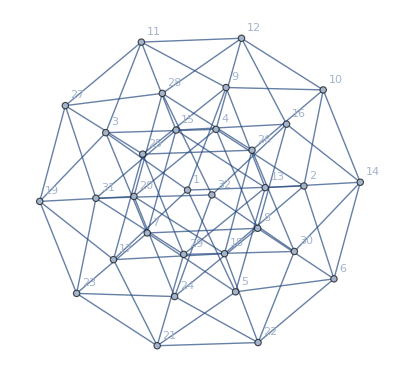

{-5,5,-3,-3,-3,-3,-3,3,3,3,3,3,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*5d Hypercube*)
G=HypercubeGraph[5,VertexLabels->"Name"]
Eigenvalues[MyAdjacencyMatrix[G]]
```

```mathematica
(*Eigenvalue 1*)
mat = Simplify[Smash[G,{21,29,13,15,9,11}]] /. L -> 1
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{31563977/20620405,6092352/4124081,598848/1212965,2121792/4124081,2121792/4124081,9677952/20620405},{6092352/4124081,3968245/4124081,289152/242593,2061120/4124081,2061120/4124081,1521984/4124081},{598848/1212965,289152/242593,712009/1212965,306576/242593,306576/242593,242448/1212965},{2121792/4124081,2061120/4124081,306576/242593,62239883/61861215,16874992/61861215,5951376/4124081},{2121792/4124081,2061120/4124081,306576/242593,16874992/61861215,62239883/61861215,5951376/4124081},{9677952/20620405,1521984/4124081,242448/1212965,5951376/4124081,5951376/4124081,22178777/20620405}}

$Aborted

$Aborted

```mathematica
(*Eigenvalue -1*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> -1
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

{{ⅇ^(-ⅈ t),0,0,0},{0,ⅇ^(-ⅈ t),0,0},{0,0,ⅇ^(-ⅈ t),0},{0,0,0,ⅇ^(-ⅈ t)}}

{{-(-1)^(3/4),0,0,0},{0,-(-1)^(3/4),0,0},{0,0,-(-1)^(3/4),0},{0,0,0,-(-1)^(3/4)}}

```mathematica
(*Eigenvalue 3*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> 3
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{3,0,0,0},{0,3,0,0},{0,0,3,0},{0,0,0,3}}

{{ⅇ^(3 ⅈ t),0,0,0},{0,ⅇ^(3 ⅈ t),0,0},{0,0,ⅇ^(3 ⅈ t),0},{0,0,0,ⅇ^(3 ⅈ t)}}

{{(-1)^(3/4),0,0,0},{0,(-1)^(3/4),0,0},{0,0,(-1)^(3/4),0},{0,0,0,(-1)^(3/4)}}

```mathematica
(*Eigenvalue -3*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> -3
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{-3,0,0,0},{0,-3,0,0},{0,0,-3,0},{0,0,0,-3}}

{{ⅇ^(-3 ⅈ t),0,0,0},{0,ⅇ^(-3 ⅈ t),0,0},{0,0,ⅇ^(-3 ⅈ t),0},{0,0,0,ⅇ^(-3 ⅈ t)}}

{{-(-1)^(1/4),0,0,0},{0,-(-1)^(1/4),0,0},{0,0,-(-1)^(1/4),0},{0,0,0,-(-1)^(1/4)}}

```mathematica
(*Eigenvalue 5*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> 5
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{393005/228073,375744/228073,178560/228073,193056/228073},{375744/228073,253965/228073,332096/228073,178560/228073},{178560/228073,332096/228073,253965/228073,375744/228073},{193056/228073,178560/228073,375744/228073,393005/228073}}

{{(ⅇ^(-(ⅈ (-771+32 √9109) t)/2887) (9109-55 √9109+(9109+55 √9109) ⅇ^((64 ⅈ √9109 t)/2887)+9109 ⅇ^((32 ⅈ (427+√9109) t)/2887)+9109 ⅇ^((32 ⅈ (-911+79 √9109) t)/228073)))/36436,-1/4 ⅇ^((11 ⅈ t)/79)+1/4 ⅇ^(5 ⅈ t)-(39 ⅇ^(-(ⅈ (-771+32 √9109) t)/2887))/(2 √9109)+(39 ⅇ^((ⅈ (771+32 √9109) t)/2887))/(2 √9109),-1/4 ⅇ^((11 ⅈ t)/79)+1/4 ⅇ^(5 ⅈ t)+(39 ⅇ^(-(ⅈ (-771+32 √9109) t)/2887))/(2 √9109)-(39 ⅇ^((ⅈ (771+32 √9109) t)/2887))/(2 √9109),(ⅇ^(-(ⅈ (-771+32 √9109) t)/2887) (-9109+55 √9109-(9109+55 √9109) ⅇ^((64 ⅈ √9109 t)/2887)+9109 ⅇ^((32 ⅈ (427+√9109) t)/2887)+9109 ⅇ^((32 ⅈ (-911+79 √9109) t)/228073)))/36436},{-1/4 ⅇ^((11 ⅈ t)/79)+1/4 ⅇ^(5 ⅈ t)-(39 ⅇ^(-(ⅈ (-771+32 √9109) t)/2887))/(2 √9109)+(39 ⅇ^((ⅈ (771+32 √9109) t)/2887))/(2 √9109),(ⅇ^(-(ⅈ (-771+32 √9109) t)/2887) (9109+55 √9109+(9109-55 √9109) ⅇ^((64 ⅈ √9109 t)/2887)+9109 ⅇ^((32 ⅈ (427+√9109) t)/2887)+9109 ⅇ^((32 ⅈ (-911+79 √9109) t)/228073)))/36436,(ⅇ^(-(ⅈ (-771+32 √9109) t)/2887) (-9109-55 √9109+(-9109+55 √9109) ⅇ^((64 ⅈ √9109 t)/2887)+9109 ⅇ^((32 ⅈ (427+√9109) t)/2887)+9109 ⅇ^((32 ⅈ (-911+79 √9109) t)/228073)))/36436,-1/4 ⅇ^((11 ⅈ t)/79)+1/4 ⅇ^(5 ⅈ t)+(39 ⅇ^(-(ⅈ (-771+32 √9109) t)/2887))/(2 √9109)-(39 ⅇ^((ⅈ (771+32 √9109) t)/2887))/(2 √9109)},{-1/4 ⅇ^((11 ⅈ t)/79)+1/4 ⅇ^(5 ⅈ t)+(39 ⅇ^(-(ⅈ (-771+32 √9109) t)/2887))/(2 √9109)-(39 ⅇ^((ⅈ (771+32 √9109) t)/2887))/(2 √9109),(ⅇ^(-(ⅈ (-771+32 √9109) t)/2887) (-9109-55 √9109+(-9109+55 √9109) ⅇ^((64 ⅈ √9109 t)/2887)+9109 ⅇ^((32 ⅈ (427+√9109) t)/2887)+9109 ⅇ^((32 ⅈ (-911+79 √9109) t)/228073)))/36436,(ⅇ^(-(ⅈ (-771+32 √9109) t)/2887) (9109+55 √9109+(9109-55 √9109) ⅇ^((64 ⅈ √9109 t)/2887)+9109 ⅇ^((32 ⅈ (427+√9109) t)/2887)+9109 ⅇ^((32 ⅈ (-911+79 √9109) t)/228073)))/36436,-1/4 ⅇ^((11 ⅈ t)/79)+1/4 ⅇ^(5 ⅈ t)-(39 ⅇ^(-(ⅈ (-771+32 √9109) t)/2887))/(2 √9109)+(39 ⅇ^((ⅈ (771+32 √9109) t)/2887))/(2 √9109)},{(ⅇ^(-(ⅈ (-771+32 √9109) t)/2887) (-9109+55 √9109-(9109+55 √9109) ⅇ^((64 ⅈ √9109 t)/2887)+9109 ⅇ^((32 ⅈ (427+√9109) t)/2887)+9109 ⅇ^((32 ⅈ (-911+79 √9109) t)/228073)))/36436,-1/4 ⅇ^((11 ⅈ t)/79)+1/4 ⅇ^(5 ⅈ t)+(39 ⅇ^(-(ⅈ (-771+32 √9109) t)/2887))/(2 √9109)-(39 ⅇ^((ⅈ (771+32 √9109) t)/2887))/(2 √9109),-1/4 ⅇ^((11 ⅈ t)/79)+1/4 ⅇ^(5 ⅈ t)-(39 ⅇ^(-(ⅈ (-771+32 √9109) t)/2887))/(2 √9109)+(39 ⅇ^((ⅈ (771+32 √9109) t)/2887))/(2 √9109),(ⅇ^(-(ⅈ (-771+32 √9109) t)/2887) (9109-55 √9109+(9109+55 √9109) ⅇ^((64 ⅈ √9109 t)/2887)+9109 ⅇ^((32 ⅈ (427+√9109) t)/2887)+9109 ⅇ^((32 ⅈ (-911+79 √9109) t)/228073)))/36436}}

{{((-1)^(771/11548) (-9109 (-1)^(529/2887) (1+(-1)^(62/79))+(9109-55 √9109) ⅇ^(-(8 ⅈ √9109 π)/2887)+(9109+55 √9109) ⅇ^((8 ⅈ √9109 π)/2887)))/36436,-1/4 (-1)^(11/316) (1+(-1)^(17/79))-(39 (-1)^(771/11548) ⅇ^(-(8 ⅈ √9109 π)/2887))/(2 √9109)+(39 (-1)^(771/11548) ⅇ^((8 ⅈ √9109 π)/2887))/(2 √9109),-1/4 (-1)^(11/316) (1+(-1)^(17/79))+(39 (-1)^(771/11548) ⅇ^(-(8 ⅈ √9109 π)/2887))/(2 √9109)-(39 (-1)^(771/11548) ⅇ^((8 ⅈ √9109 π)/2887))/(2 √9109),((-1)^(771/11548) (-9109 (-1)^(529/2887) (1+(-1)^(62/79))+(-9109+55 √9109) ⅇ^(-(8 ⅈ √9109 π)/2887)-(9109+55 √9109) ⅇ^((8 ⅈ √9109 π)/2887)))/36436},{-1/4 (-1)^(11/316) (1+(-1)^(17/79))-(39 (-1)^(771/11548) ⅇ^(-(8 ⅈ √9109 π)/2887))/(2 √9109)+(39 (-1)^(771/11548) ⅇ^((8 ⅈ √9109 π)/2887))/(2 √9109),((-1)^(771/11548) (-9109 (-1)^(529/2887) (1+(-1)^(62/79))+(9109+55 √9109) ⅇ^(-(8 ⅈ √9109 π)/2887)+(9109-55 √9109) ⅇ^((8 ⅈ √9109 π)/2887)))/36436,((-1)^(771/11548) (-9109 (-1)^(529/2887) (1+(-1)^(62/79))-(9109+55 √9109) ⅇ^(-(8 ⅈ √9109 π)/2887)+(-9109+55 √9109) ⅇ^((8 ⅈ √9109 π)/2887)))/36436,-1/4 (-1)^(11/316) (1+(-1)^(17/79))+(39 (-1)^(771/11548) ⅇ^(-(8 ⅈ √9109 π)/2887))/(2 √9109)-(39 (-1)^(771/11548) ⅇ^((8 ⅈ √9109 π)/2887))/(2 √9109)},{-1/4 (-1)^(11/316) (1+(-1)^(17/79))+(39 (-1)^(771/11548) ⅇ^(-(8 ⅈ √9109 π)/2887))/(2 √9109)-(39 (-1)^(771/11548) ⅇ^((8 ⅈ √9109 π)/2887))/(2 √9109),((-1)^(771/11548) (-9109 (-1)^(529/2887) (1+(-1)^(62/79))-(9109+55 √9109) ⅇ^(-(8 ⅈ √9109 π)/2887)+(-9109+55 √9109) ⅇ^((8 ⅈ √9109 π)/2887)))/36436,((-1)^(771/11548) (-9109 (-1)^(529/2887) (1+(-1)^(62/79))+(9109+55 √9109) ⅇ^(-(8 ⅈ √9109 π)/2887)+(9109-55 √9109) ⅇ^((8 ⅈ √9109 π)/2887)))/36436,-1/4 (-1)^(11/316) (1+(-1)^(17/79))-(39 (-1)^(771/11548) ⅇ^(-(8 ⅈ √9109 π)/2887))/(2 √9109)+(39 (-1)^(771/11548) ⅇ^((8 ⅈ √9109 π)/2887))/(2 √9109)},{((-1)^(771/11548) (-9109 (-1)^(529/2887) (1+(-1)^(62/79))+(-9109+55 √9109) ⅇ^(-(8 ⅈ √9109 π)/2887)-(9109+55 √9109) ⅇ^((8 ⅈ √9109 π)/2887)))/36436,-1/4 (-1)^(11/316) (1+(-1)^(17/79))+(39 (-1)^(771/11548) ⅇ^(-(8 ⅈ √9109 π)/2887))/(2 √9109)-(39 (-1)^(771/11548) ⅇ^((8 ⅈ √9109 π)/2887))/(2 √9109),-1/4 (-1)^(11/316) (1+(-1)^(17/79))-(39 (-1)^(771/11548) ⅇ^(-(8 ⅈ √9109 π)/2887))/(2 √9109)+(39 (-1)^(771/11548) ⅇ^((8 ⅈ √9109 π)/2887))/(2 √9109),((-1)^(771/11548) (-9109 (-1)^(529/2887) (1+(-1)^(62/79))+(9109-55 √9109) ⅇ^(-(8 ⅈ √9109 π)/2887)+(9109+55 √9109) ⅇ^((8 ⅈ √9109 π)/2887)))/36436}}

```mathematica
(*Eigenvalue -5*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> -5
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{-393005/228073,375744/228073,-178560/228073,193056/228073},{375744/228073,-253965/228073,332096/228073,-178560/228073},{-178560/228073,332096/228073,-253965/228073,375744/228073},{193056/228073,-178560/228073,375744/228073,-393005/228073}}

{{1/4 ⅇ^(-5 ⅈ t) (1+ⅇ^((384 ⅈ t)/79)+(1+55/(√9109)) ⅇ^(-(32 ⅈ (-427+√9109) t)/2887)+(1-55/(√9109)) ⅇ^((32 ⅈ (427+√9109) t)/2887)),1/4 ⅇ^(-5 ⅈ t) (-1+ⅇ^((384 ⅈ t)/79)-(78 ⅇ^(-(32 ⅈ (-427+√9109) t)/2887))/(√9109)+(78 ⅇ^((32 ⅈ (427+√9109) t)/2887))/(√9109)),1/4 ⅇ^(-5 ⅈ t) (1-ⅇ^((384 ⅈ t)/79)-(78 ⅇ^(-(32 ⅈ (-427+√9109) t)/2887))/(√9109)+(78 ⅇ^((32 ⅈ (427+√9109) t)/2887))/(√9109)),1/4 ⅇ^(-5 ⅈ t) (-1-ⅇ^((384 ⅈ t)/79)+(1+55/(√9109)) ⅇ^(-(32 ⅈ (-427+√9109) t)/2887)+(1-55/(√9109)) ⅇ^((32 ⅈ (427+√9109) t)/2887))},{1/4 ⅇ^(-5 ⅈ t) (-1+ⅇ^((384 ⅈ t)/79)-(78 ⅇ^(-(32 ⅈ (-427+√9109) t)/2887))/(√9109)+(78 ⅇ^((32 ⅈ (427+√9109) t)/2887))/(√9109)),(ⅇ^(-(2 ⅈ (7603+16 √9109) t)/2887) ((9109-55 √9109) ⅇ^(5 ⅈ t)+(9109+55 √9109) ⅇ^((5 ⅈ+(64 ⅈ √9109)/2887) t)+9109 ⅇ^((ⅈ (771+32 √9109) t)/2887)+9109 ⅇ^((ⅈ (1169517+2528 √9109) t)/228073)))/36436,(ⅇ^(-(2 ⅈ (7603+16 √9109) t)/2887) ((9109-55 √9109) ⅇ^(5 ⅈ t)+(9109+55 √9109) ⅇ^((5 ⅈ+(64 ⅈ √9109)/2887) t)-9109 ⅇ^((ⅈ (771+32 √9109) t)/2887)-9109 ⅇ^((ⅈ (1169517+2528 √9109) t)/228073)))/36436,1/4 ⅇ^(-5 ⅈ t) (1-ⅇ^((384 ⅈ t)/79)-(78 ⅇ^(-(32 ⅈ (-427+√9109) t)/2887))/(√9109)+(78 ⅇ^((32 ⅈ (427+√9109) t)/2887))/(√9109))},{1/4 ⅇ^(-5 ⅈ t) (1-ⅇ^((384 ⅈ t)/79)-(78 ⅇ^(-(32 ⅈ (-427+√9109) t)/2887))/(√9109)+(78 ⅇ^((32 ⅈ (427+√9109) t)/2887))/(√9109)),(ⅇ^(-(2 ⅈ (7603+16 √9109) t)/2887) ((9109-55 √9109) ⅇ^(5 ⅈ t)+(9109+55 √9109) ⅇ^((5 ⅈ+(64 ⅈ √9109)/2887) t)-9109 ⅇ^((ⅈ (771+32 √9109) t)/2887)-9109 ⅇ^((ⅈ (1169517+2528 √9109) t)/228073)))/36436,(ⅇ^(-(2 ⅈ (7603+16 √9109) t)/2887) ((9109-55 √9109) ⅇ^(5 ⅈ t)+(9109+55 √9109) ⅇ^((5 ⅈ+(64 ⅈ √9109)/2887) t)+9109 ⅇ^((ⅈ (771+32 √9109) t)/2887)+9109 ⅇ^((ⅈ (1169517+2528 √9109) t)/228073)))/36436,1/4 ⅇ^(-5 ⅈ t) (-1+ⅇ^((384 ⅈ t)/79)-(78 ⅇ^(-(32 ⅈ (-427+√9109) t)/2887))/(√9109)+(78 ⅇ^((32 ⅈ (427+√9109) t)/2887))/(√9109))},{1/4 ⅇ^(-5 ⅈ t) (-1-ⅇ^((384 ⅈ t)/79)+(1+55/(√9109)) ⅇ^(-(32 ⅈ (-427+√9109) t)/2887)+(1-55/(√9109)) ⅇ^((32 ⅈ (427+√9109) t)/2887)),1/4 ⅇ^(-5 ⅈ t) (1-ⅇ^((384 ⅈ t)/79)-(78 ⅇ^(-(32 ⅈ (-427+√9109) t)/2887))/(√9109)+(78 ⅇ^((32 ⅈ (427+√9109) t)/2887))/(√9109)),1/4 ⅇ^(-5 ⅈ t) (-1+ⅇ^((384 ⅈ t)/79)-(78 ⅇ^(-(32 ⅈ (-427+√9109) t)/2887))/(√9109)+(78 ⅇ^((32 ⅈ (427+√9109) t)/2887))/(√9109)),1/4 ⅇ^(-5 ⅈ t) (1+ⅇ^((384 ⅈ t)/79)+(1+55/(√9109)) ⅇ^(-(32 ⅈ (-427+√9109) t)/2887)+(1-55/(√9109)) ⅇ^((32 ⅈ (427+√9109) t)/2887))}}

{{-((-1)^(10777/11548) ⅇ^(-(8 ⅈ √9109 π)/2887) (9109+55 √9109+9109 (-1)^(7288/228073) (1+(-1)^(62/79)) ⅇ^((8 ⅈ √9109 π)/2887)+(9109-55 √9109) ⅇ^((16 ⅈ √9109 π)/2887)))/36436,((-1)^(3/4) (-9109 (1+(-1)^(17/79))+78 (-1)^(529/2887) √9109 ⅇ^(-(8 ⅈ √9109 π)/2887)-78 (-1)^(529/2887) √9109 ⅇ^((8 ⅈ √9109 π)/2887)))/36436,((-1)^(3/4) (9109 (1+(-1)^(17/79))+78 (-1)^(529/2887) √9109 ⅇ^(-(8 ⅈ √9109 π)/2887)-78 (-1)^(529/2887) √9109 ⅇ^((8 ⅈ √9109 π)/2887)))/36436,((-1)^(10777/11548) ⅇ^(-(8 ⅈ √9109 π)/2887) (-9109-55 √9109+9109 (-1)^(7288/228073) (1+(-1)^(62/79)) ⅇ^((8 ⅈ √9109 π)/2887)+(-9109+55 √9109) ⅇ^((16 ⅈ √9109 π)/2887)))/36436},{((-1)^(3/4) (-9109 (1+(-1)^(17/79))+78 (-1)^(529/2887) √9109 ⅇ^(-(8 ⅈ √9109 π)/2887)-78 (-1)^(529/2887) √9109 ⅇ^((8 ⅈ √9109 π)/2887)))/36436,-((-1)^(10777/11548) ⅇ^(-(8 ⅈ √9109 π)/2887) (9109-55 √9109+9109 (-1)^(7288/228073) (1+(-1)^(62/79)) ⅇ^((8 ⅈ √9109 π)/2887)+(9109+55 √9109) ⅇ^((16 ⅈ √9109 π)/2887)))/36436,((-1)^(10777/11548) ⅇ^(-(8 ⅈ √9109 π)/2887) (-9109+55 √9109+9109 (-1)^(7288/228073) (1+(-1)^(62/79)) ⅇ^((8 ⅈ √9109 π)/2887)-(9109+55 √9109) ⅇ^((16 ⅈ √9109 π)/2887)))/36436,((-1)^(3/4) (9109 (1+(-1)^(17/79))+78 (-1)^(529/2887) √9109 ⅇ^(-(8 ⅈ √9109 π)/2887)-78 (-1)^(529/2887) √9109 ⅇ^((8 ⅈ √9109 π)/2887)))/36436},{((-1)^(3/4) (9109 (1+(-1)^(17/79))+78 (-1)^(529/2887) √9109 ⅇ^(-(8 ⅈ √9109 π)/2887)-78 (-1)^(529/2887) √9109 ⅇ^((8 ⅈ √9109 π)/2887)))/36436,((-1)^(10777/11548) ⅇ^(-(8 ⅈ √9109 π)/2887) (-9109+55 √9109+9109 (-1)^(7288/228073) (1+(-1)^(62/79)) ⅇ^((8 ⅈ √9109 π)/2887)-(9109+55 √9109) ⅇ^((16 ⅈ √9109 π)/2887)))/36436,-((-1)^(10777/11548) ⅇ^(-(8 ⅈ √9109 π)/2887) (9109-55 √9109+9109 (-1)^(7288/228073) (1+(-1)^(62/79)) ⅇ^((8 ⅈ √9109 π)/2887)+(9109+55 √9109) ⅇ^((16 ⅈ √9109 π)/2887)))/36436,((-1)^(3/4) (-9109 (1+(-1)^(17/79))+78 (-1)^(529/2887) √9109 ⅇ^(-(8 ⅈ √9109 π)/2887)-78 (-1)^(529/2887) √9109 ⅇ^((8 ⅈ √9109 π)/2887)))/36436},{((-1)^(10777/11548) ⅇ^(-(8 ⅈ √9109 π)/2887) (-9109-55 √9109+9109 (-1)^(7288/228073) (1+(-1)^(62/79)) ⅇ^((8 ⅈ √9109 π)/2887)+(-9109+55 √9109) ⅇ^((16 ⅈ √9109 π)/2887)))/36436,((-1)^(3/4) (9109 (1+(-1)^(17/79))+78 (-1)^(529/2887) √9109 ⅇ^(-(8 ⅈ √9109 π)/2887)-78 (-1)^(529/2887) √9109 ⅇ^((8 ⅈ √9109 π)/2887)))/36436,((-1)^(3/4) (-9109 (1+(-1)^(17/79))+78 (-1)^(529/2887) √9109 ⅇ^(-(8 ⅈ √9109 π)/2887)-78 (-1)^(529/2887) √9109 ⅇ^((8 ⅈ √9109 π)/2887)))/36436,-((-1)^(10777/11548) ⅇ^(-(8 ⅈ √9109 π)/2887) (9109+55 √9109+9109 (-1)^(7288/228073) (1+(-1)^(62/79)) ⅇ^((8 ⅈ √9109 π)/2887)+(9109-55 √9109) ⅇ^((16 ⅈ √9109 π)/2887)))/36436}}

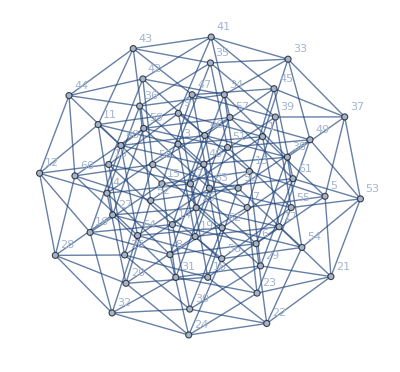

{-6,6,-4,-4,-4,-4,-4,-4,4,4,4,4,4,4,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*6d Hypercube*)
G=HypercubeGraph[6,VertexLabels->"Name"]
Eigenvalues[MyAdjacencyMatrix[G]]
```

```mathematica
(*Eigenvalue 2*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> 2
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}}

{{ⅇ^(2 ⅈ t),0,0,0},{0,ⅇ^(2 ⅈ t),0,0},{0,0,ⅇ^(2 ⅈ t),0},{0,0,0,ⅇ^(2 ⅈ t)}}

{{ⅈ,0,0,0},{0,ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,ⅈ}}

```mathematica
(*Eigenvalue -2*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> -2
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{-2,0,0,0},{0,-2,0,0},{0,0,-2,0},{0,0,0,-2}}

{{ⅇ^(-2 ⅈ t),0,0,0},{0,ⅇ^(-2 ⅈ t),0,0},{0,0,ⅇ^(-2 ⅈ t),0},{0,0,0,ⅇ^(-2 ⅈ t)}}

{{-ⅈ,0,0,0},{0,-ⅈ,0,0},{0,0,-ⅈ,0},{0,0,0,-ⅈ}}

```mathematica
(*Eigenvalue 4*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> 4
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{4,0,0,0},{0,4,0,0},{0,0,4,0},{0,0,0,4}}

{{ⅇ^(4 ⅈ t),0,0,0},{0,ⅇ^(4 ⅈ t),0,0},{0,0,ⅇ^(4 ⅈ t),0},{0,0,0,ⅇ^(4 ⅈ t)}}

{{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
(*Eigenvalue -4*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> -4
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{-4,0,0,0},{0,-4,0,0},{0,0,-4,0},{0,0,0,-4}}

{{ⅇ^(-4 ⅈ t),0,0,0},{0,ⅇ^(-4 ⅈ t),0,0},{0,0,ⅇ^(-4 ⅈ t),0},{0,0,0,ⅇ^(-4 ⅈ t)}}

{{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
(*Eigenvalue 6*)
mat = Simplify[Smash[G,{1,2,4,8}]] /. L -> 6
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> π/4]
```

{{41186/20091,38080/20091,19840/20091,21440/20091},{38080/20091,28706/20091,33920/20091,19840/20091},{19840/20091,33920/20091,28706/20091,38080/20091},{21440/20091,19840/20091,38080/20091,41186/20091}}

{{(ⅇ^(-(320 ⅈ √530 t)/6697) ((530-13 √530) ⅇ^((2422 ⅈ t)/6697)+530 ⅇ^((6 ⅈ+(320 ⅈ √530)/6697) t)+(530+13 √530) ⅇ^((2 ⅈ (1211+320 √530) t)/6697)+530 ⅇ^((2 ⅈ (2353+480 √530) t)/20091)))/2120,-1/4 ⅇ^((26 ⅈ t)/111)+1/4 ⅇ^(6 ⅈ t)-(19 ⅇ^(-(2 ⅈ (-1211+160 √530) t)/6697))/(4 √530)+(19 ⅇ^((2 ⅈ (1211+160 √530) t)/6697))/(4 √530),-1/4 ⅇ^((26 ⅈ t)/111)+1/4 ⅇ^(6 ⅈ t)+(19 ⅇ^(-(2 ⅈ (-1211+160 √530) t)/6697))/(4 √530)-(19 ⅇ^((2 ⅈ (1211+160 √530) t)/6697))/(4 √530),(ⅇ^(-(320 ⅈ √530 t)/6697) ((-530+13 √530) ⅇ^((2422 ⅈ t)/6697)+530 ⅇ^((6 ⅈ+(320 ⅈ √530)/6697) t)-(530+13 √530) ⅇ^((2 ⅈ (1211+320 √530) t)/6697)+530 ⅇ^((2 ⅈ (2353+480 √530) t)/20091)))/2120},{-1/4 ⅇ^((26 ⅈ t)/111)+1/4 ⅇ^(6 ⅈ t)-(19 ⅇ^(-(2 ⅈ (-1211+160 √530) t)/6697))/(4 √530)+(19 ⅇ^((2 ⅈ (1211+160 √530) t)/6697))/(4 √530),(ⅇ^(-(320 ⅈ √530 t)/6697) ((530+13 √530) ⅇ^((2422 ⅈ t)/6697)+530 ⅇ^((6 ⅈ+(320 ⅈ √530)/6697) t)+(530-13 √530) ⅇ^((2 ⅈ (1211+320 √530) t)/6697)+530 ⅇ^((2 ⅈ (2353+480 √530) t)/20091)))/2120,(ⅇ^(-(320 ⅈ √530 t)/6697) (-((530+13 √530) ⅇ^((2422 ⅈ t)/6697))+530 ⅇ^((6 ⅈ+(320 ⅈ √530)/6697) t)+(-530+13 √530) ⅇ^((2 ⅈ (1211+320 √530) t)/6697)+530 ⅇ^((2 ⅈ (2353+480 √530) t)/20091)))/2120,-1/4 ⅇ^((26 ⅈ t)/111)+1/4 ⅇ^(6 ⅈ t)+(19 ⅇ^(-(2 ⅈ (-1211+160 √530) t)/6697))/(4 √530)-(19 ⅇ^((2 ⅈ (1211+160 √530) t)/6697))/(4 √530)},{-1/4 ⅇ^((26 ⅈ t)/111)+1/4 ⅇ^(6 ⅈ t)+(19 ⅇ^(-(2 ⅈ (-1211+160 √530) t)/6697))/(4 √530)-(19 ⅇ^((2 ⅈ (1211+160 √530) t)/6697))/(4 √530),(ⅇ^(-(320 ⅈ √530 t)/6697) (-((530+13 √530) ⅇ^((2422 ⅈ t)/6697))+530 ⅇ^((6 ⅈ+(320 ⅈ √530)/6697) t)+(-530+13 √530) ⅇ^((2 ⅈ (1211+320 √530) t)/6697)+530 ⅇ^((2 ⅈ (2353+480 √530) t)/20091)))/2120,(ⅇ^(-(320 ⅈ √530 t)/6697) ((530+13 √530) ⅇ^((2422 ⅈ t)/6697)+530 ⅇ^((6 ⅈ+(320 ⅈ √530)/6697) t)+(530-13 √530) ⅇ^((2 ⅈ (1211+320 √530) t)/6697)+530 ⅇ^((2 ⅈ (2353+480 √530) t)/20091)))/2120,-1/4 ⅇ^((26 ⅈ t)/111)+1/4 ⅇ^(6 ⅈ t)-(19 ⅇ^(-(2 ⅈ (-1211+160 √530) t)/6697))/(4 √530)+(19 ⅇ^((2 ⅈ (1211+160 √530) t)/6697))/(4 √530)},{(ⅇ^(-(320 ⅈ √530 t)/6697) ((-530+13 √530) ⅇ^((2422 ⅈ t)/6697)+530 ⅇ^((6 ⅈ+(320 ⅈ √530)/6697) t)-(530+13 √530) ⅇ^((2 ⅈ (1211+320 √530) t)/6697)+530 ⅇ^((2 ⅈ (2353+480 √530) t)/20091)))/2120,-1/4 ⅇ^((26 ⅈ t)/111)+1/4 ⅇ^(6 ⅈ t)+(19 ⅇ^(-(2 ⅈ (-1211+160 √530) t)/6697))/(4 √530)-(19 ⅇ^((2 ⅈ (1211+160 √530) t)/6697))/(4 √530),-1/4 ⅇ^((26 ⅈ t)/111)+1/4 ⅇ^(6 ⅈ t)-(19 ⅇ^(-(2 ⅈ (-1211+160 √530) t)/6697))/(4 √530)+(19 ⅇ^((2 ⅈ (1211+160 √530) t)/6697))/(4 √530),(ⅇ^(-(320 ⅈ √530 t)/6697) ((530-13 √530) ⅇ^((2422 ⅈ t)/6697)+530 ⅇ^((6 ⅈ+(320 ⅈ √530)/6697) t)+(530+13 √530) ⅇ^((2 ⅈ (1211+320 √530) t)/6697)+530 ⅇ^((2 ⅈ (2353+480 √530) t)/20091)))/2120}}

{{(530 (-ⅈ+(-1)^(13/222))+(-1)^(1211/13394) (530-13 √530) ⅇ^(-(80 ⅈ √530 π)/6697)+(-1)^(1211/13394) (530+13 √530) ⅇ^((80 ⅈ √530 π)/6697))/2120,-ⅈ/4-1/4 (-1)^(13/222)-(19 (-1)^(1211/13394) ⅇ^(-(80 ⅈ √530 π)/6697))/(4 √530)+(19 (-1)^(1211/13394) ⅇ^((80 ⅈ √530 π)/6697))/(4 √530),-ⅈ/4-1/4 (-1)^(13/222)+(19 (-1)^(1211/13394) ⅇ^(-(80 ⅈ √530 π)/6697))/(4 √530)-(19 (-1)^(1211/13394) ⅇ^((80 ⅈ √530 π)/6697))/(4 √530),(530 (-ⅈ+(-1)^(13/222))+(-1)^(1211/13394) (-530+13 √530) ⅇ^(-(80 ⅈ √530 π)/6697)-(-1)^(1211/13394) (530+13 √530) ⅇ^((80 ⅈ √530 π)/6697))/2120},{-ⅈ/4-1/4 (-1)^(13/222)-(19 (-1)^(1211/13394) ⅇ^(-(80 ⅈ √530 π)/6697))/(4 √530)+(19 (-1)^(1211/13394) ⅇ^((80 ⅈ √530 π)/6697))/(4 √530),(530 (-ⅈ+(-1)^(13/222))+(-1)^(1211/13394) (530+13 √530) ⅇ^(-(80 ⅈ √530 π)/6697)+(-1)^(1211/13394) (530-13 √530) ⅇ^((80 ⅈ √530 π)/6697))/2120,(530 (-ⅈ+(-1)^(13/222))-(-1)^(1211/13394) (530+13 √530) ⅇ^(-(80 ⅈ √530 π)/6697)+(-1)^(1211/13394) (-530+13 √530) ⅇ^((80 ⅈ √530 π)/6697))/2120,-ⅈ/4-1/4 (-1)^(13/222)+(19 (-1)^(1211/13394) ⅇ^(-(80 ⅈ √530 π)/6697))/(4 √530)-(19 (-1)^(1211/13394) ⅇ^((80 ⅈ √530 π)/6697))/(4 √530)},{-ⅈ/4-1/4 (-1)^(13/222)+(19 (-1)^(1211/13394) ⅇ^(-(80 ⅈ √530 π)/6697))/(4 √530)-(19 (-1)^(1211/13394) ⅇ^((80 ⅈ √530 π)/6697))/(4 √530),(530 (-ⅈ+(-1)^(13/222))-(-1)^(1211/13394) (530+13 √530) ⅇ^(-(80 ⅈ √530 π)/6697)+(-1)^(1211/13394) (-530+13 √530) ⅇ^((80 ⅈ √530 π)/6697))/2120,(530 (-ⅈ+(-1)^(13/222))+(-1)^(1211/13394) (530+13 √530) ⅇ^(-(80 ⅈ √530 π)/6697)+(-1)^(1211/13394) (530-13 √530) ⅇ^((80 ⅈ √530 π)/6697))/2120,-ⅈ/4-1/4 (-1)^(13/222)-(19 (-1)^(1211/13394) ⅇ^(-(80 ⅈ √530 π)/6697))/(4 √530)+(19 (-1)^(1211/13394) ⅇ^((80 ⅈ √530 π)/6697))/(4 √530)},{(530 (-ⅈ+(-1)^(13/222))+(-1)^(1211/13394) (-530+13 √530) ⅇ^(-(80 ⅈ √530 π)/6697)-(-1)^(1211/13394) (530+13 √530) ⅇ^((80 ⅈ √530 π)/6697))/2120,-ⅈ/4-1/4 (-1)^(13/222)+(19 (-1)^(1211/13394) ⅇ^(-(80 ⅈ √530 π)/6697))/(4 √530)-(19 (-1)^(1211/13394) ⅇ^((80 ⅈ √530 π)/6697))/(4 √530),-ⅈ/4-1/4 (-1)^(13/222)-(19 (-1)^(1211/13394) ⅇ^(-(80 ⅈ √530 π)/6697))/(4 √530)+(19 (-1)^(1211/13394) ⅇ^((80 ⅈ √530 π)/6697))/(4 √530),(530 (-ⅈ+(-1)^(13/222))+(-1)^(1211/13394) (530-13 √530) ⅇ^(-(80 ⅈ √530 π)/6697)+(-1)^(1211/13394) (530+13 √530) ⅇ^((80 ⅈ √530 π)/6697))/2120}}